# FEW vs WaSABI 1PAT1R Implementation

## Python setup. PySaBI? FEWSaBI

Executing python from within conda environment “1pat1r” having installed FEW- edit path to your own executable.

```mathematica
session=StartExternalSession[<|"System"->"Python","Executable"->"/Users/joshmathews/anaconda3/envs/1pat1r/bin/python"|>];
```

```mathematica
py=ExternalEvaluate[session];
```

## Functions for formatting python code.

Below passing code_String=”print(“hello world “)” will not work (fundamental issue with Mathematica syntax). Need to replace to code_String=”print(\“hello world \“)”.

```mathematica
(*Convert a multi-line Python string into a list of individual py["..."] calls*)PyLines[code_String]:=StringJoin[Riffle["py[\""<>#<>"\"]"&/@Select[StringSplit[code,"\n"],StringLength[#]>0&],";\n"]]<>";"

(*Convert a multi-line Python string into a single py["...\n...\n..."] call*)
PyBlock[code_String]:="py[\""<>StringReplace[StringTrim[code],{"\n"->"\\n","\""->"\\\"","\\"->"\\\\"}]<>"\"];"
```

Modulo strings, you should be able to copy python code directly here using these functions. It won’t display plots in the notebook, but you can save figures as files.

#### Example:

Using a single line

```mathematica
pythoncode="print(\"hello world\")"
```

print("hello world")

Returns a string so it does not evaluate and you can copy and paste the code, removing the outer “” manually.

```mathematica
PyLines[pythoncode]
```

py["print("hello world")"];

Using a block with indentation etc:

```mathematica
code="results = []
for i in range(10):
    results.append(i**2)
print(results)"

PyBlock[code]
```

results = []
for i in range(10):
    results.append(i**2)
print(results)

py["results = []\nfor i in range(10):\n    results.append(i**2)\nprint(results)"];

Since the python code contains no strings, we can evaluate using ToExpression:

```mathematica
PyBlock[code]//ToExpression
```

[0, 1, 4, 9, 16, 25, 36, 49, 64, 81]

## Comparing the amplitudes against WaSABI

#### Getting FEW amplitudes:

Importing stuff

```mathematica
py["from few.trajectory.inspiral import EMRIInspiral"];
py["from few.trajectory.ode.IPAT1R import Trajectory1PAT1R"];
py["import matplotlib.pyplot as plt"];
py["import numpy as np"];
py["from few.amplitude.ampinterp1d import AmpInterp1PAT1R"];
py["amp = AmpInterp1PAT1R()"]
```

Evaluating the amplitude pieces

```mathematica
GetAmpsAtr0[r0_,l_,m_]:=Module[{string,amps0PA,amps1PA,ampschi2,ampschi1,ampsdeltam,pos},
pos=Flatten[Position[Flatten[Table[{ll,mm},{ll,2,5},{mm,1,ll}],1],{l,m}]][[1]];
string="amp.get_amplitudes_single_piece(0,"<>ToString[r0]<>", 0.0, 1.0,";
amps0PA=Flatten[Normal[py[string<>"data_key=\"0PA\")"]]][[5;;]][[pos]];
amps1PA=Flatten[Normal[py[string<>"data_key=\"1PA\")"]]][[5;;]][[pos]];
ampschi2=Flatten[Normal[py[string<>"data_key=\"1PAchi2\")"]]][[5;;]][[pos]];
ampschi1=Flatten[Normal[py[string<>"data_key=\"1PAchi1\")"]]][[5;;]][[pos]];
ampsdeltam=Flatten[Normal[py[string<>"data_key=\"1PAdeltam\")"]]][[5;;]][[pos]];
<|"0PA"->amps0PA,"1PA"->amps1PA,"chi2"->ampschi2,"chi1"->ampschi1,"δm"->ampsdeltam|>
]
```

```mathematica
GetAmpsAtr0[7.0,2,1]
```

<|0PA→-0.0339536-0.121127 ⅈ,1PA→0.0521078+0.26001 ⅈ,chi2→-0.0101694-0.036284 ⅈ,chi1→0.0231815+0.0834066 ⅈ,δm→-0.0578895-0.134309 ⅈ|>

```mathematica
GetAmpsAtr0Combined[r0_,l_,m_,ν_,chit1_,chit2_,deltam1_]:=Module[{modestring,string1},
py["nu="<>ToString[ν]];
py["chit1="<>ToString[chit1]];
py["chit2="<>ToString[chit2]];
py["delta_m1="<>ToString[deltam1]];
modestring="("<>ToString[l]<>","<>ToString[m]<>",0,0)";
string1="amp.get_amplitudes(0,"<>ToString[r0]<>", 0.0, 1.0, nu=nu, chit=chit1,chit2=chit2, delta_m1=delta_m1,specific_modes=["<>modestring<>"])["<>modestring<>"]";
Normal[py[string1]]
]
```

```mathematica
GetAmpsAtr0Combined2[r0_,l_,m_,ν_,chit1_,chit2_,deltam1_]:=Module[{modestring,string1},
py["nu="<>ToString[ν]];
py["chit1="<>ToString[chit1]];
py["chit2="<>ToString[chit2]];
py["delta_m1="<>ToString[deltam1]];
modestring="("<>ToString[l]<>","<>ToString[m]<>",0,0)";
string1="amp.get_amplitudes(0,"<>ToString[r0]<>", 0.0, 1.0, nu=nu, chit=chit1,chit2=chit2, delta_m1=delta_m1, specific_modes=["<>modestring<>"], zero_PA_amps_only = True )["<>modestring<>"]";
Normal[py[string1]]
]
```

```mathematica
GetAmpsAtr0Combined[7.0,2,2,0.1,0.5,0.5,0.6]
```

{0.747372-0.293311 ⅈ}

```mathematica
GetAmpsAtr0Combined2[7.0,2,2,0.1,0.5,0.5,0.6]
```

{0.796233-0.264339 ⅈ}

```mathematica
GetAmpsAtr0[7.0,2,2]
```

<|0PA→0.796233-0.264339 ⅈ,1PA→-0.0699758-0.365173 ⅈ,chi2→-0.0391612+0.0130044 ⅈ,chi1→-0.112016+0.0304906 ⅈ,δm→0.562091-0.236696 ⅈ|>

#### Getting WaSABI amplitudes

```mathematica
<<WaSABI`
```

```mathematica
GetWaSABIAmps[r0_,l_,m_]:=Module[{fullamp,modestring,amps0PA,amps1PA,ampschi2,ampschi1,ampsdeltam},
modestring="("<>ToString[l]<>","<>ToString[m]<>")";
fullamp=If[OddQ[m],1/(√(1-4ν))(*Accounting for resummed odd amp vs raw data*)(WaSABI`Waveform`Private`GetAmplitudes["1PAT1R",{}]/.{ WaSABI`Inspiral`Model1PAT1R`ν->ν,WaSABI`Inspiral`Model1PAT1R`Ω->√(1/r0^3),WaSABI`Inspiral`Model1PAT1R`M->1,WaSABI`Inspiral`Model1PAT1R`χt1->χt1,WaSABI`Inspiral`Model1PAT1R`χt2->χt2,WaSABI`Inspiral`Model1PAT1R`δm->δm})[modestring],(WaSABI`Waveform`Private`GetAmplitudes["1PAT1R",{}]/.{ WaSABI`Inspiral`Model1PAT1R`ν->ν,WaSABI`Inspiral`Model1PAT1R`Ω->√(1/r0^3),WaSABI`Inspiral`Model1PAT1R`M->1,WaSABI`Inspiral`Model1PAT1R`χt1->χt1,WaSABI`Inspiral`Model1PAT1R`χt2->χt2,WaSABI`Inspiral`Model1PAT1R`δm->δm})[modestring]];
amps0PA=Coefficient[fullamp,ν]/.{χt1->0,χt2->0};
amps1PA=If[OddQ[m],(Coefficient[fullamp,ν^2]/.{χt1->0,χt2->0,δm->0})-2*amps0PA,(Coefficient[fullamp,ν^2]/.{χt1->0,χt2->0,δm->0})];
ampschi1=Coefficient[fullamp,χt1]/.{ν->1};
ampschi2=Coefficient[fullamp,χt2]/.{ν->1};
ampsdeltam=Coefficient[fullamp,δm]/.{ν->1};
<|"0PA"->amps0PA,"1PA"->amps1PA,"chi2"->ampschi2,"chi1"->ampschi1,"δm"->ampsdeltam|>
]
```

```mathematica
GetWaSABIAmpsCombined[r0_,l_,m_]:=Module[{fullamp,modestring},
modestring="("<>ToString[l]<>","<>ToString[m]<>")";
fullamp=(WaSABI`Waveform`Private`GetAmplitudes["1PAT1R",{}]/.{ WaSABI`Inspiral`Model1PAT1R`ν->ν,WaSABI`Inspiral`Model1PAT1R`Ω->√(1/r0^3),WaSABI`Inspiral`Model1PAT1R`M->1,WaSABI`Inspiral`Model1PAT1R`χt1->χt1,WaSABI`Inspiral`Model1PAT1R`χt2->χt2,WaSABI`Inspiral`Model1PAT1R`δm->δm})[modestring]
]
```

#### Comparisons of individual amplitude terms --- See only 1PA (5,1) mode being noteworthy.

```mathematica
1-GetWaSABIAmps[7.0,2,2]/(-GetAmpsAtr0[7.0,2,2])
```

<|0PA→-1.57629×10^-12-1.20298×10^-12 ⅈ,1PA→-3.53028×10^-8-1.59374×10^-7 ⅈ,chi2→-2.23177×10^-12-5.6205×10^-13 ⅈ,chi1→-9.25628×10^-9+1.17494×10^-8 ⅈ,δm→1.95722×10^-9+1.76569×10^-9 ⅈ|>

```mathematica
ampcheck[l_,m_]:=Table[{r0,Abs[1-GetWaSABIAmps[r0,l,m]/(-GetAmpsAtr0[r0,l,m])]},{r0,6.25,30,0.01}]
```

```mathematica
Monitor[Do[amprelerr[l,m]=ampcheck[l,m];,{l,2,5},{m,1,l}],{l,m}]
```

```mathematica
keys=Keys[amprelerr[2,2][[1,2]]];
Do[
series[l,m]=Table[{key,Table[{row[[1]],row[[2]][key]},{row,amprelerr[l,m]}]},{key,keys}];,{l,2,5},{m,1,l}]
```

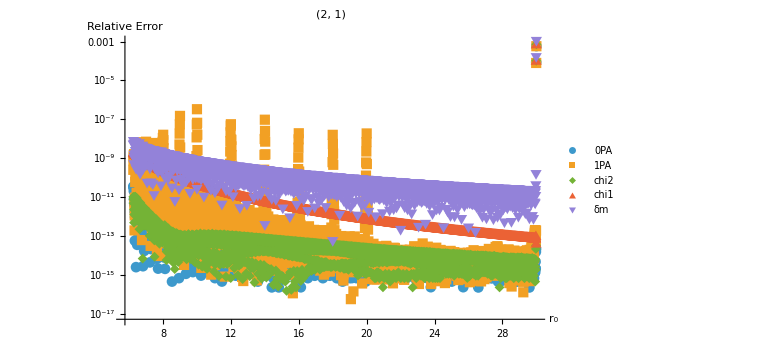

```mathematica
With[{l=2,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

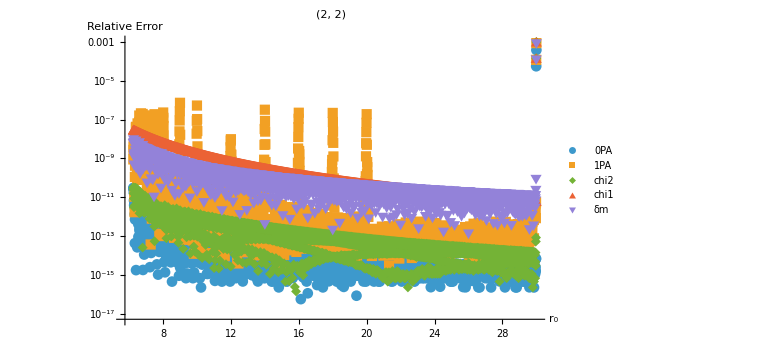

```mathematica
With[{l=2,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

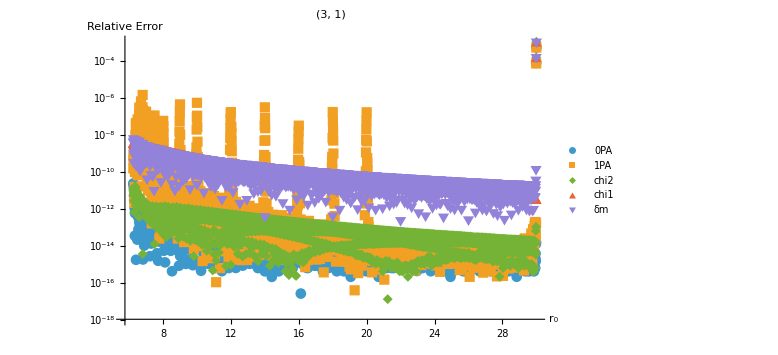

```mathematica
With[{l=3,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

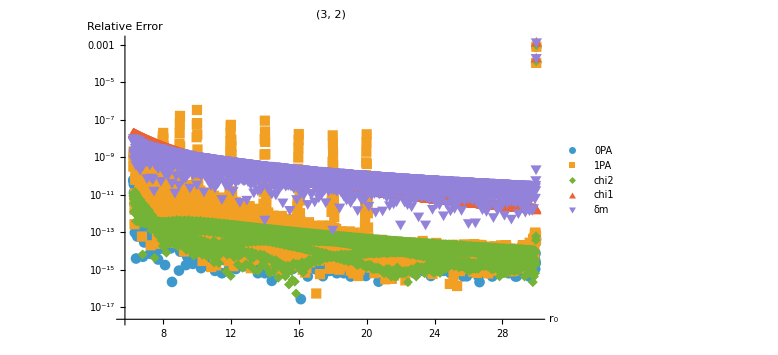

```mathematica
With[{l=3,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

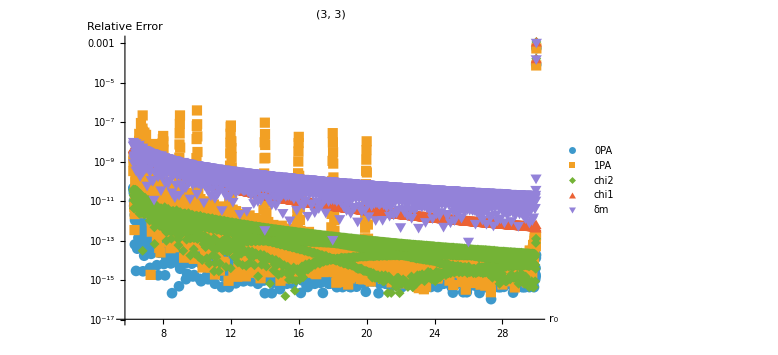

```mathematica
With[{l=3,m=3},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

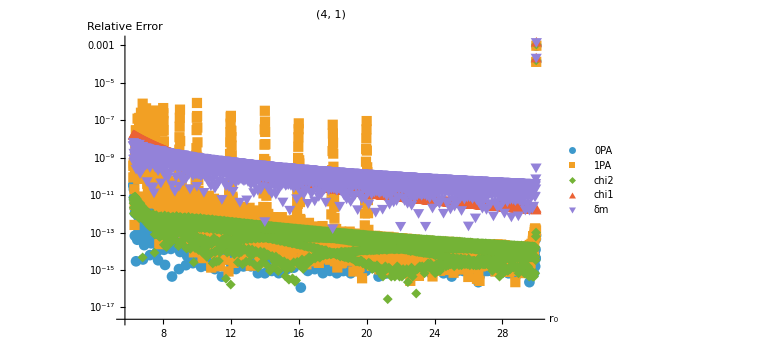

```mathematica
With[{l=4,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

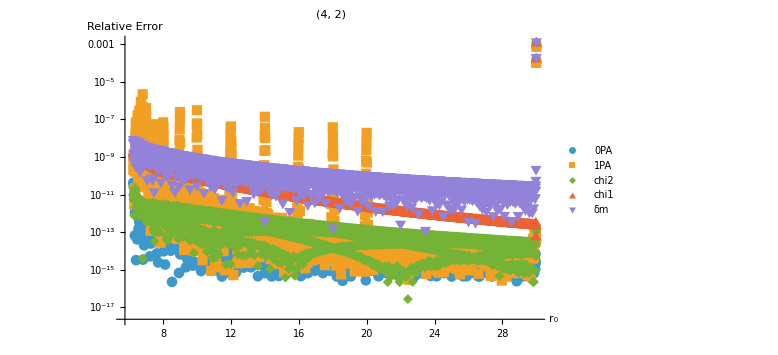

```mathematica
With[{l=4,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

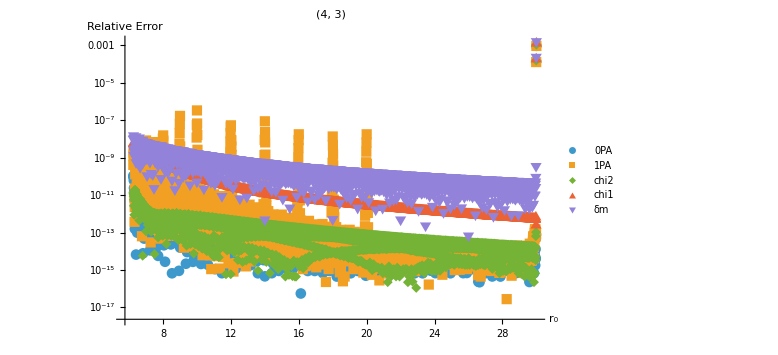

```mathematica
With[{l=4,m=3},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

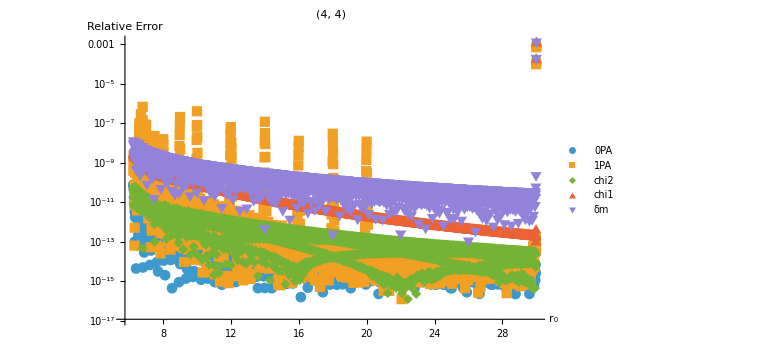

```mathematica
With[{l=4,m=4},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

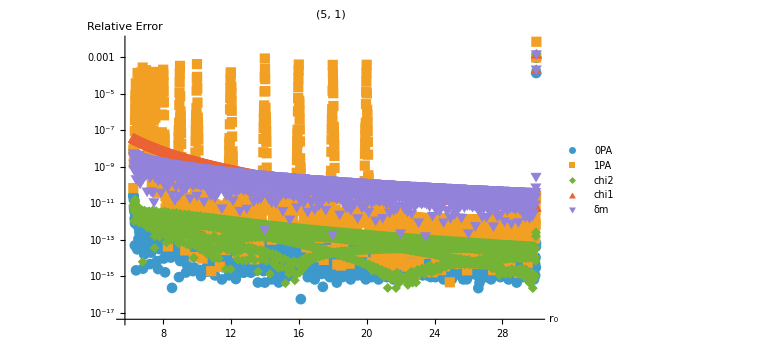

```mathematica
With[{l=5,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

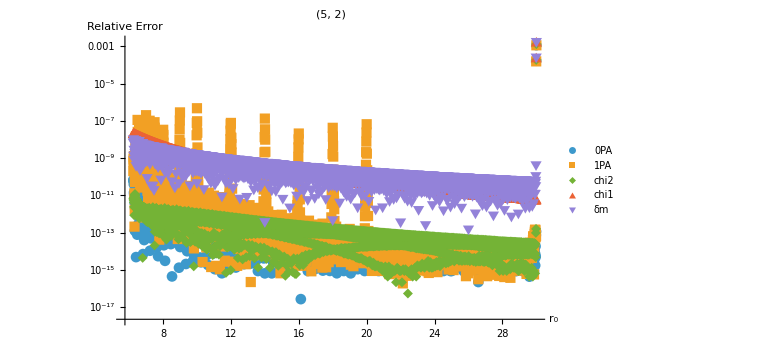

```mathematica
With[{l=5,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

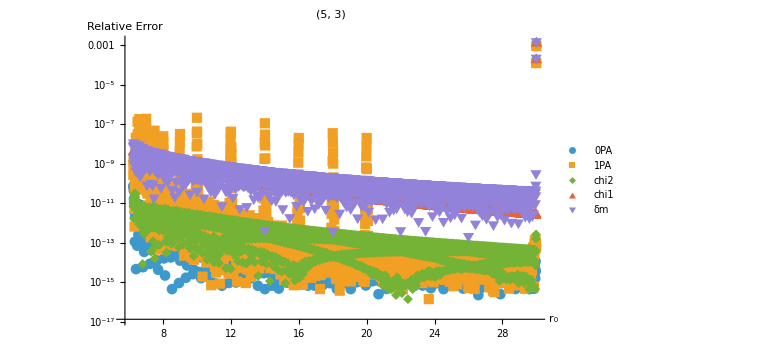

```mathematica
With[{l=5,m=3},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

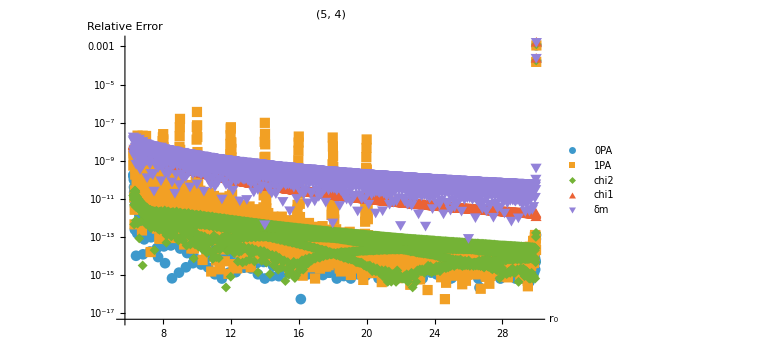

```mathematica
With[{l=5,m=4},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

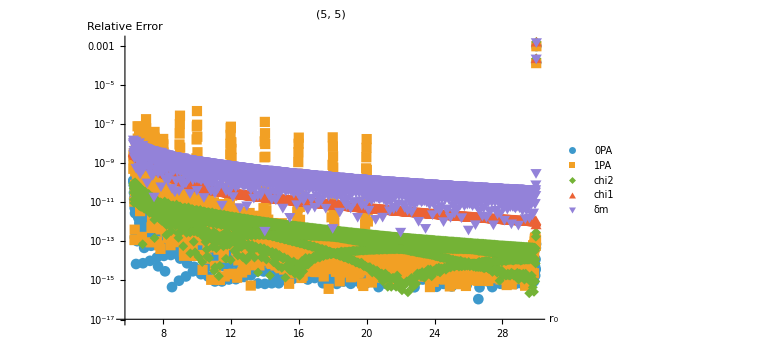

```mathematica
With[{l=5,m=5},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

#### Comparison of combined amplitudes

```mathematica
GetWaSABIAmpsCombined[7.0,2,2]/.{ν->0.1,χt1->0.5,χt2->0.5,δm->0.6}
```

-0.0747372+0.0293311 ⅈ

Note few amplitudes scale waveform by ν:

```mathematica
combinecheckWasabi=(1/ν)GetWaSABIAmpsCombined[7.0,2,1]/.{ν->0.1,χt1->0.5,χt2->0.5,δm->0.6}
```

0.0251751+0.0804409 ⅈ

```mathematica
combinecheckFEW=-GetAmpsAtr0Combined[7.0,2,1,0.1,0.5,0.5,0.6]
```

{0.0251751+0.0804409 ⅈ}

```mathematica
1-(combinecheckWasabi/combinecheckFEW)
```

{2.04455×10^-9+3.34198×10^-10 ⅈ}

```mathematica
combinecheckWasabi2=(1/ν)GetWaSABIAmpsCombined[7.0,2,1]/.{ν->0.1,χt1->-0.5,χt2->0.5,δm->0.6}
```

0.0431314+0.145047 ⅈ

```mathematica
combinecheckFEW2=-GetAmpsAtr0Combined[7.0,2,1,0.1,-0.5,0.5,0.6]
```

{0.0431314+0.145047 ⅈ}

```mathematica
1-(combinecheckWasabi2/combinecheckFEW2)
```

{8.98495×10^-10+3.70073×10^-10 ⅈ}

So we have checked the individual interpolations and that the amplitudes are combined correctly.

## Comparing the inspiral against WaSABI

Put me here.

## Comparing the waveform against WaSABI

#### FEW waveforms in Mathematica:

```mathematica
PyBlock["import numpy as np
import matplotlib.pyplot as plt
from few.waveform import Waveform1PAT1R, FastKerrEccentricEquatorialFlux

m1 = 1e6       
m2 = 10      
chi1  = 1e-5
a = chi1 
p0 = 9.0      
theta = np.pi / 3.0   
phi   = 0.0           
chi2  = 0.1 
dt = 1.  
T  = 1   

WF1PAT1R = Waveform1PAT1R()
h = WF1PAT1R(m1, m2, a, p0, theta, phi, chi2, dt=dt, T=T, mode_selection='all')"]//ToExpression
```

```mathematica
waveformFEW=py["h.tolist()"];
```

```mathematica
dt=1;
tFEW=Range[0,(Length[waveformFEW]-1)]*dt;
```

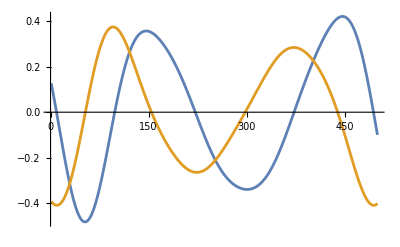

```mathematica
Show[ListPlot[Re[waveformFEW][[-500;;]],Joined->True,PlotStyle->ColorData[97,1]],ListPlot[Im[waveformFEW][[-500;;]],Joined->True,PlotStyle->ColorData[97,2]]]
```

#### Mode summed WaSABI waveforms with the same time:

Need to use spin weighted spheroidal harmonics

```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<WaSABI`
```

Relevant SI units:

```mathematica
py["
from few.utils import constants as c
for k, v in vars(c).items():
    if not k.startswith('_') and not callable(v):
        print(f'{k} = {v}')
"]//ToExpression
```

ASTRONOMICAL_YEAR = 31558149.763545595

GM_SUN = 1.3271244e+20

PARSEC = 3.085677581491367e+16

SPEED_OF_LIGHT = 299792458.0

SUN_SCHWARZSCHILD_RADIUS = 2953.2500761002498

YRSID_SI = 31558149.763545595

MTSUN_SI = 4.9254909476412675e-06

MRSUN_SI = 1476.6250380501249

Gpc = 3.0856775814913673e+25

PI = 3.141592653589793

```mathematica
m1val=10^6; (*mass in Msun*)
m2val=10;   (*mass in Msun*)
χ1val=N[10^-5];
p0val=N[9];
θval=N[π/3];
χ2val=0.1;
νval=N[(m1val*m2val)/(m1val+m2val)^2];
Mval=N[(m1val+m2val)];
χt1val=N[1/2(1+√(1-4νval))χ1val];
χt2val=N[1/2(1-√(1-4νval))χ2val];
```

```mathematica
MTSUN=4.9254909476412675*10^(-06);  (*GM_sun/c^3 in seconds*)
MRSUN=1476.6250380501249;     (*GM_sun/c^2 in metres*)
```

```mathematica
wasabiWaveform=BinaryInspiral[<|"Ω"->√(1/p0val^3),"ϕ"->0,"ν"->νval,"M"->Mval,"χt1"->χt1val,"χt2"->χt2val,"δm"->0|>,"Model"->"1PAT1R","Precision"->12,"Accuracy"->12];
```

InterpolatingFunction::dmval: Input value {9.9998×10^-6,9.9999×10^-6,9.9999×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
slm[l_,m_]:=SpinWeightedSphericalHarmonicY[-2,l,m,θval,0]
```

```mathematica
waveform[ts_]:=-(1)*(Sum[wasabiWaveform["Waveform"][l,m][ts/(MTSUN)]*slm[l,m],{l,2,5},{m,1,l}]+Sum[wasabiWaveform["Waveform"][l,m][ts/(MTSUN)]*slm[l,m],{l,2,5},{m,-l,-1}]);
```

#### Comparison:

Warning: Careful of FEW waveform normalisation when distance is not specified (need to multiply FEW waveform by ν*M)

```mathematica
(*Tick helper*)niceFrameTicks[min_,max_,n_:5]:={#,NumberForm[N[#],3]}&/@FindDivisions[{min,max},n]

(*Plot options*)
plotOpts=Sequence[AspectRatio->1/4,Frame->True,BaseStyle->{FontSize->14},FrameLabel->{{"Re[h]",None},{"t (s)",None}},LabelStyle->Directive[Black,14]];

(*Early inspiral*)
first1000s=Show[Plot[Re[waveform[t]],{t,0,1000}],ListPlot[Transpose[{tFEW,Re[νval*Mval*waveformFEW]}][[;;1000]],Joined->True,PlotStyle->Directive[ColorData[97,2],Dashed]],plotOpts,FrameTicks->{{Automatic,None},{niceFrameTicks[0,1000],None}}];

(*Late inspiral*)
last1000s=Show[Plot[Re[waveform[t]],{t,22314134,22315134}],ListPlot[Transpose[{tFEW,Re[νval*Mval*waveformFEW]}][[22314134;;]],Joined->True,PlotStyle->Directive[ColorData[97,2],Dashed]],plotOpts,FrameTicks->{{Automatic,None},{niceFrameTicks[22314134,22315134],None}}];

(*Combined labelled grid*)
GraphicsGrid[{{Labeled[first1000s,Style["Early inspiral (t = 0–1000 s)",14,Bold],Top]},{Labeled[last1000s,Style["Late inspiral (t = 22314134–22315134 s)",14,Bold],Top]}},Spacings->{0,10},ImageSize->800]
```

-Graphics-

Now looking at the waveform difference (slow):

```mathematica
(*Tick helper*)niceFrameTicks[min_,max_,n_:5]:={#,NumberForm[N[#],3]}&/@FindDivisions[{min,max},n]

(*Plot options*)
plotOpts=Sequence[AspectRatio->1/4,Frame->True,BaseStyle->{FontSize->14},FrameLabel->{{"Re[Δh]",None},{"t (s)",None}},LabelStyle->Directive[Black,14]];

(*Precompute only the needed segments*)
tFEWFirst=tFEW[[;;1000]];
tFEWLast=tFEW[[22314134;;]];

diffFirst=Re[νval*Mval*waveformFEW[[;;1000]]]-(Re[waveform[#]]&/@tFEWFirst);
diffLast=Re[νval*Mval*waveformFEW[[22314134;;]]]-(Re[waveform[#]]&/@tFEWLast);

(*Early difference*)
first1000sDiff=ListPlot[Transpose[{tFEWFirst,diffFirst}],Joined->True,PlotStyle->ColorData[97,3],plotOpts,FrameTicks->{{Automatic,None},{niceFrameTicks[0,1000],None}}];

(*Late difference*)
last1000sDiff=ListPlot[Transpose[{tFEWLast,diffLast}],Joined->True,PlotStyle->ColorData[97,3],plotOpts,FrameTicks->{{Automatic,None},{niceFrameTicks[22314134,22315134],None}}];

(*Combined labelled grid*)
GraphicsGrid[{{Labeled[first1000sDiff,Style["Early inspiral (t = 0–1000 s)",14,Bold],Top]},{Labeled[last1000sDiff,Style["Late inspiral (t = 22314134–22315134 s)",14,Bold],Top]}},Spacings->{0,10},ImageSize->800]
```

-Graphics-

In the late inspiral, the difference has grown. Check trajectory via looking at phase difference - the error does not seem to be caused by the wasabi integration settings.

```mathematica
PyBlock["
from few.trajectory.inspiral import EMRIInspiral
from few.trajectory.ode.IPAT1R import Trajectory1PAT1R

traj = EMRIInspiral(func=Trajectory1PAT1R)

t_traj, p_traj, e_traj, x_traj, Phi_phi_traj, Phi_theta_traj, Phi_r_traj, deltaM_traj, deltachit1_traj = traj(
    m1, m2,
    a,        
    p0,
    0.0,      
    1.0,      
    chi2,     
    T=T,
    dt=dt
)
"]//ToExpression
```

```mathematica
tTraj=py["t_traj.tolist()"];
pTraj=py["p_traj.tolist()"];
PhiPhiTraj=py["Phi_phi_traj.tolist()"];
```

We find the phase accuracy is consistent with the ODE integrator err tolerance, so it’s unlikely to be the WaSABI integration settings here:

```mathematica
Δϕ=DeleteCases[DeleteCases[Table[{tTraj[[i]],1-(wasabiWaveform["Trajectory"]["ϕ"][tTraj[[i]]/(MTSUN)])/(PhiPhiTraj[[i]])},{i,1,Length[tTraj]}],{_,Indeterminate}],{_,ComplexInfinity}];
```

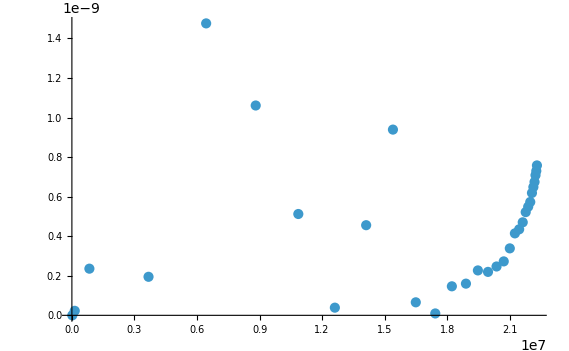

```mathematica
ListPlot[Abs[Δϕ],PlotRange->All]
```